```mathematica
(*Module that solves for a field given an intial guess for the field value. The argument is a list: {initial guess of field (double), and shooter (boolean)}. If shooter is true, the method returns a pair of points {ϕ[end of integration] - ϕcosmological,ϕ0 (initial guess)} for ease of plotting. If shooter is false, the method returns the interpolation functions as a list {phi -> interior solution,ϕe -> exterior solution.*)
```

```mathematica
backgroundsolution[args_]:= Module[
{startI = 0.000001,
endI = 1.001,
startE = 1,
endE = 1000,
Λ = .010,
ϕcosmological = args[[1]]/10000,
ρ = 10,
Rscaled = 1,
Shooter = args[[2]],
ϕ0 = args[[1]]},

backgroundsolutioninterior= NDSolve[{1/Rscaled^2 D[ϕ[r],r,r]+2/(r Rscaled)D[ϕ[r],r]+2/Λ^2(4/(r Rscaled)D[ϕ[r],r]+ 2/(r^2 Rscaled^2)(D[ϕ[r],r])^2)==8π ρ,ϕ'[startI] ==0,ϕ[startI] ==  ϕ0},
ϕ,{r,startI,endI}];
backgroundsolutionexterior=NDSolve[{1/Rscaled^2 D[ϕe[r],r,r]+2/(r Rscaled)D[ϕe[r],r]+2/Λ^2(4/(r Rscaled)D[ϕe[r],r]+ 2/(r^2 Rscaled^2)(D[ϕe[r],r])^2)==0,ϕe[startE] ==  ϕ[1]/.backgroundsolutioninterior,ϕe'[startE] == ϕ'[1]/.backgroundsolutioninterior},
ϕe,{r,startE,endE}];
Proximity= (ϕe[endE]/.backgroundsolutionexterior) -ϕcosmological;
If[Shooter,Prepend[Proximity,ϕ0],{backgroundsolutioninterior,backgroundsolutionexterior}]
]
```

```mathematica
(*Solutions = Table[backgroundsolution[{x,True}],{x,Range[Trialstart,Trialend,Trialstep]}];*)
```

```mathematica
(*Solutions = Parallelize[Table[backgroundsolution[{x,True}],{x,Range[Trialstart,Trialend,Trialstep]}]];*)
```

```mathematica
(*Shooter method evaluation and plotting for range from Trialstart to Trialend for step size Trialstep. Plots point {Subscript[ϕ, 0],ϕ-ϕcosmological (as defined in backgroundsolution)}*)
```

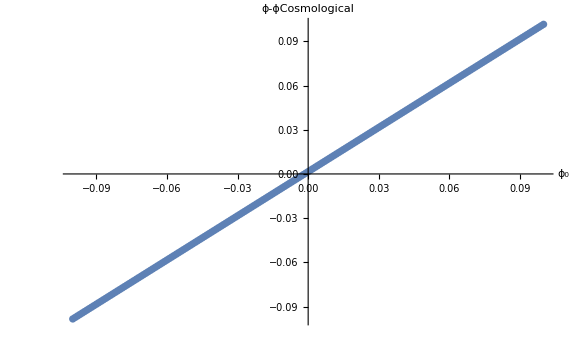

```mathematica
With[{Trialend = .1,
Trialstart = -.1,
Trialstep = .001},ListPlot[Parallelize[Table[backgroundsolution[{x,True}],{x,Range[Trialstart,Trialend,Trialstep]}]],AxesLabel->{"ϕ_0","ϕ-ϕCosmological"},ImageSize->Large]]
```

```mathematica
(*Evaluation and plotting of a specific intial guess*)
```

```mathematica
sol=backgroundsolution[{0.1,False}]
```

{{{ϕ→                             -6
InterpolatingFunction[{{1. 10  , 1.001}}, <>]}},{{ϕe→InterpolatingFunction[{{1., 1000.}}, <>]}}}

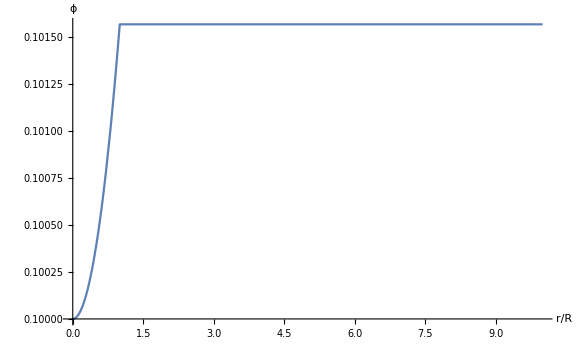

```mathematica
Plot[Piecewise[{{ϕ[r]/.sol[[1]],r<1},{ϕe[r]/.sol[[2]],r>1}}],{r,0.000001,10},ImageSize->Large,AxesLabel->{"r/R","ϕ"}]
```